Ryan Foundoulis
605107291
ryanfoundoulis@gmail.com
HW 2

i)

{{y[t]→H+(g m (m-ⅇ^(-(b t)/m) m-b t))/b^2}}

ii)

H+(g m (m-ⅇ^(-(b t)/m) m-b t))/b^2

iii)

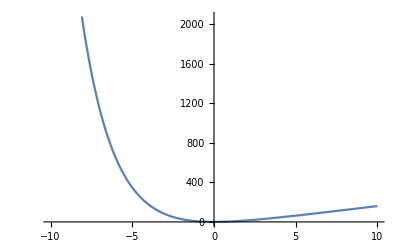

```mathematica
(* Problem 1 *) 
Remove["Global`*"]

	"i)"
	solution = DSolve[{y''[t]+(b/m)y'[t]+g == 0, y'[0]==0, y[0]==H}, y[t], t] //FullSimplify

	"ii)"
	(* Building a usable function f[x] that represents our y[t] function *)
	f[x_] = y[t]/.solution[[1]];
	f[x] /. x-> t

	"iii)"
	g = -10;m = 10;b = 5; H=0;
	
	Plot[f[x], {t, -10, 10}]
```

i)

difEq1 = k q1[t]-k q2[t]+m1 q1''[t]==-k L

difEq2 = -k q1[t]+k q2[t]+m2 q2''[t]==k L

constr1 = q1'[0]==0

constr2 = q2'[0]==0

constr3 = q1[0]==0

constr4 = q2[0]==L+δ

ii)

listOfEqs = {k q1[t]-k q2[t]+m1 q1''[t]==-k L,-k q1[t]+k q2[t]+m2 q2''[t]==k L,q1'[0]==0,q2'[0]==0,q1[0]==0,q2[0]==L+δ}

iii)

listOfFuncts = {q1[t],q2[t]}

iv)

{{q1[t]→-(m2 δ (-1+Cosh[(k (m1+m2) t)/(√(-k m1 m2 (m1+m2)))]))/(m1+m2),q2[t]→(L (m1+m2)+m2 δ+m1 δ Cosh[(k (m1+m2) t)/(√(-k m1 m2 (m1+m2)))])/(m1+m2)}}

v)

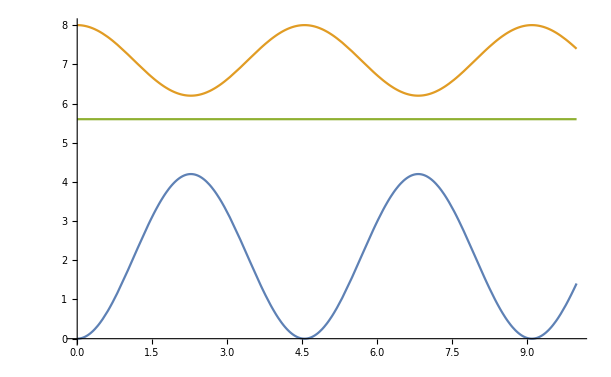

```mathematica
(* Problem 2 *) 
	Remove["Global`*"]
	"i)"
	(* System of Eq.s *)

	difEq1  = m1 q1''[t] + k q1[t] - k q2[t] == -k L;
	difEq2 = m2 q2''[t] - k q1[t] + k q2[t] == k L;

	Print["difEq1 = ", difEq1]
	Print["difEq2 = ", difEq2]

	(* Constrainsts *)

	constr1 = q1'[0] == 0;
	constr2 = q2'[0] == 0;
	constr3 = q1[0] == 0;
	constr4 = q2 [0] == L + δ;

	Print["constr1 = ", constr1]
	Print["constr2 = ", constr2]
	Print["constr3 = ", constr3]
	Print["constr4 = ", constr4]

	"ii)" 
	listOfEqs = {difEq1, difEq2, constr1, constr2, constr3, constr4};

	Print["listOfEqs = ", listOfEqs]

	"iii)"
	listOfFuncts = {q1[t], q2[t]};

	Print["listOfFuncts = ", listOfFuncts]

	"iv)"
	sol = DSolve[listOfEqs, listOfFuncts, t] //FullSimplify

	"v)"
	 L = 5; m1 = 3; m2 = 7; k = 4; δ = 3;

	q1a[t_] = q1[t] /. sol;
	q2a[t_] = q2[t] /. sol;
	qCoM[t_] = (q1a[t]m1+q2a[t]m2) / (m1+m2);
	Plot[{q1a[t],q2a[t], qCoM[t]}, {t, 0, 10}]
```

i)

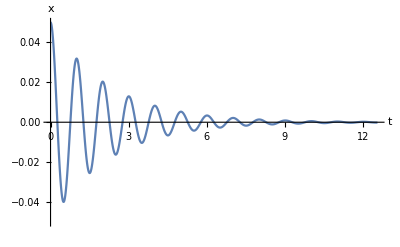

ii)

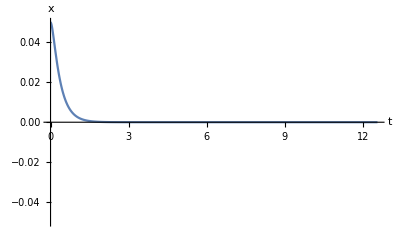

iii)

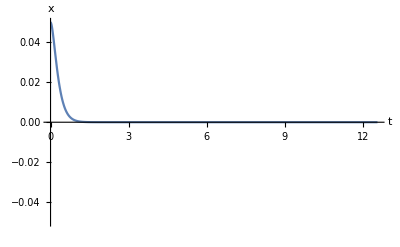

I chose to use the approximation of 44/7-0.002 for pi in the β = 2π in order to avoid the 1/0 issue that was found in the first attempt.
I could not get the β reassignment to work in the individual case, which is why I did the approximation, but in the manipulation case I managed to get it to work.

I chose to use the approximation of 44/7-0.002 for pi in the β = 2π in order to avoid the 1/0 issue that was found in the first attempt

```mathematica
(* Problem 3 *)

	Remove["Global`*"]

	osc[β_] = x''[t] + 2 β x'[t] + ω0^2 x[t] == 0;

	sol[β_] := DSolve[{osc[β], x[0] == A0, x'[0]==0}, x[t], t][[1]] //FullSimplify;

	tmin = 0;
	tmax = 4 Pi;

	xmin = -.05;
	xmax = .05;
	(* Creating usable function *)
	x1a[t_] := x[t] /. sol[β][[1]];
	


	range = {{tmin, tmax}, { xmin, xmax}};
	label = {"t", "x"};


	"i)"

	x2[t_] = x1a[t] /. A0 -> .05  /. ω0 -> 2 Pi /. β -> Pi / 7;
	
	Plot[x2[t], {t,tmin,tmax}, PlotRange-> range, AxesLabel->label]

	"ii)"

	x3[β_] = x1a[t] /. A0 -> .05  /. ω0 -> 2 Pi /. β -> 5 Pi / 2;

	Plot[x3[β], {t,tmin,tmax}, PlotRange-> range, AxesLabel->label]



	"iii)" (* FIX THIS ISSUE *)

	x4[β_] := x1a[t] /. A0 -> .05  /. ω0 -> 2 Pi;

	Plot[Evaluate[x4[β] /. β-> 44/7], {t,tmin,tmax}, PlotRange-> range, AxesLabel->label]

		Print["I chose to use the approximation of 44/7-0.002 for pi in the β = 2π in order to avoid the 1/0 issue that was found in the first attempt.
I could not get the β reassignment to work in the individual case, which is why I did the approximation, but in the manipulation case I managed to get it to work."]


	

βlo = 0;
βhi = 4 Pi;
			traj[β_] := Plot[Evaluate[x[t] /. sol[β] /. A0 -> .05  /. ω0 -> 2 Pi], {t,tmin,tmax}, PlotRange-> range, AxesLabel->label];

	Manipulate[traj[β], {β,βlo, βhi,0.1}]
```

i)

{-(a ⅇ^(-t (β+√(β^2-ω0^2))) ((-1+ⅇ^(2 t √(β^2-ω0^2))) β+(1+ⅇ^(2 t √(β^2-ω0^2))-2 ⅇ^(t (β+√((β-ω0) (β+ω0))))) √(β^2-ω0^2)))/(2 ω0^2 √((β-ω0) (β+ω0)))}

{ⅇ^(-t (β+√(β^2-ω0^2))) (C[1]+ⅇ^(2 t √(β^2-ω0^2)) C[2])}

ii)

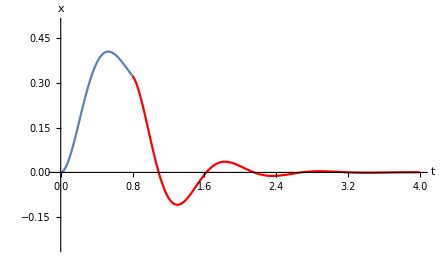

```mathematica
(* Problem 4 *)
Remove["Global`*"]

f = 0.2;
tot = 4;
forcetime = f tot;

(* Organizing EQ's *)
dampedDrivenOsc = x''[t]+2β x'[t] + ω0^2 x[t] == F[t];
dampedOsc =  y''[t]+2β y'[t] + ω0^2 y[t] == 0;
F[t_] = a;


solution1 = DSolve[{dampedDrivenOsc,x[0]==0, x'[0]==0}, x[t], t] //FullSimplify;

	g[t_] = x[t] /. solution1;

solution2 = DSolve[dampedOsc, y[t], t] // FullSimplify;

	h[t_] = y[t] /. solution2;

	"i)"

	g[t]
	h[t]

	"ii)"

	g1[t_] = g[t] /. β -> ω0 /3 /. ω0 -> 2 Pi /. a-> 12  /. f-> 0.2 //FullSimplify;

	h = g1[forcetime]; (* Starting height of the second graph *)
	j = g1'[forcetime]; (* Starting velocity of the second graph *)
	
	solution3 = DSolve[{dampedOsc, y[forcetime]==h, y'[forcetime] == j}, y[t], t] // FullSimplify;
	h1[t_] = y[t] /. solution3;
	h1a[t_] = h1[t]/. β -> ω0 /3 /. ω0 -> 2 Pi;

(* β -> ω0 /3 /. ω0 -> 2 Pi //FullSimplify*)

	tmin = -.05;
	tmax = 4;
	xmin =  -.25;
	xmax = .5;

	range = {{tmin, tmax}, { xmin, xmax}};
	label = {"t", "x"};

	plot1 = Plot[g1[t], {t, 0, forcetime}, PlotRange-> range, AxesLabel->label, PlotStyle->Lightblue];
	plot2 = Plot[h1a[t], {t,forcetime, 4}, PlotRange-> range, AxesLabel->label, PlotStyle->Red];

	Show[plot1, plot2]
```